```mathematica
Load["MH0", "MH2"];
```

Testing 1

Example 1

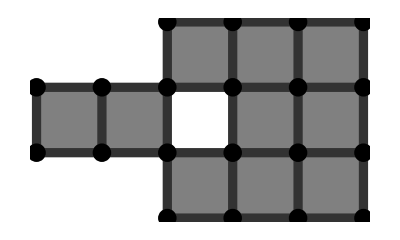
{0.00103385,-Graphics-}

```mathematica
arrC={{0,0,1,1,1},{1,1,0,1,1},{0,0,1,1,1}};
showCC2D[buildCC2D[arrC]]//AbsoluteTiming
```

Example 2

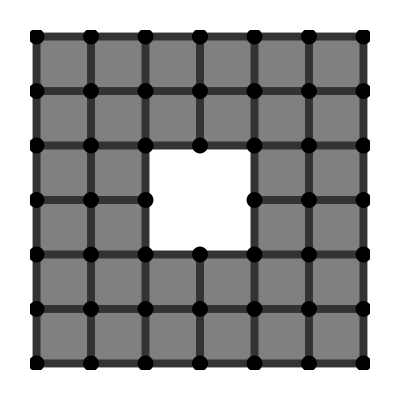
{0.00302131,-Graphics-}

```mathematica
arrRing={{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,0,0,1,1},{1,1,0,0,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1}};
showCC2D[buildCC2D[arrRing]]//AbsoluteTiming
```

Example 3

```mathematica
horse4=threshold[Reverse[ImportGray["M2/horse_64.png"]],N[100/255]];
horse4=buildCC2D[horse4];//AbsoluteTiming
```

{0.0731645,Null}

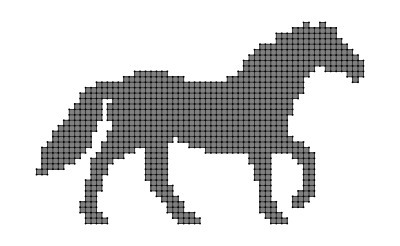

```mathematica
showCC2D[horse4]
```

Testing 2

Example 1

```mathematica
arrC3D={{{0,0},{0,0},{1,0},{1,0},{1,0}},{{1,0},{1,0},{0,0},{1,0},{1,0}},{{0,0},{0,0},{1,0},{1,0},{1,0}}};
showCC3DExt[buildCC3D[arrC3D]]//AbsoluteTiming
```

{0.00489353,-Graphics3D-}

```mathematica
Ring3DCC=buildCC3D[{
	{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}},
	{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}},
	{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}},
	{{1,1},{1,1},{1,1},{0,0},{0,0},{1,1},{1,1},{1,1}},
	{{1,1},{1,1},{1,1},{0,0},{0,0},{1,1},{1,1},{1,1}},
	{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}},
	{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}},
	{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}}
}];//AbsoluteTiming
```

{0.0201835,Null}

```mathematica
showCC3DExt[Ring3DCC]
```

-Graphics3D-

```mathematica
tShape6=Get["M2/tshape.dat"];
tShape6=buildCC3D[tShape6];//AbsoluteTiming
```

{7.23387,Null}

```mathematica
showCC3DExt[tShape6]
```

-Graphics3D-

Testing 3

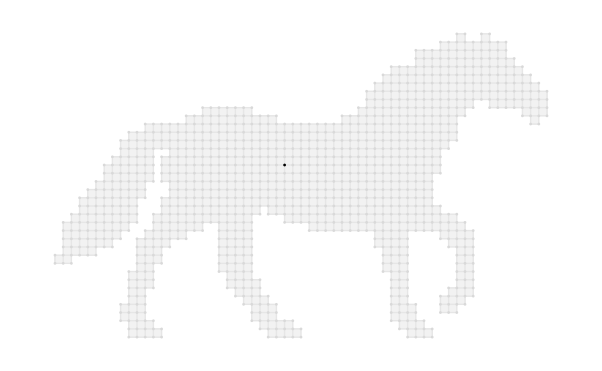
{0.258643,-Graphics-}

```mathematica
showCC2D[thinExhaustive[horse4],horse4]//AbsoluteTiming
```

```mathematica
showCC3DExt[thinExhaustive[Ring3DCC]]//AbsoluteTiming
```

{0.0494152,-Graphics3D-}

```mathematica
showCC3D[thinExhaustive[tShape6],tShape6]//AbsoluteTiming
```

{1.92022,-Graphics3D-}

Testing 4

Example 1

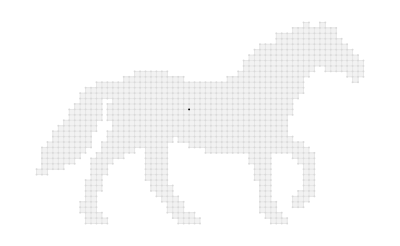
{0.576417,-Graphics-}

```mathematica
showCC2D[thin[horse4,{{Infinity,1},{Infinity,1}}],horse4]//AbsoluteTiming
```

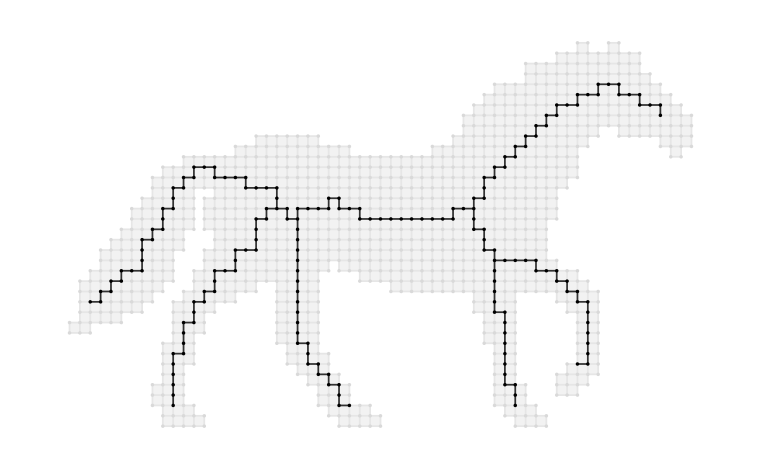
{0.307142,-Graphics-}

```mathematica
showCC2D[thin[horse4,{{5,.5},{Infinity,1}}],horse4]//AbsoluteTiming
```

```mathematica
showCC3D[thin[tShape6,{{Infinity,1},{Infinity,1}}],tShape6]//AbsoluteTiming
```

{8.34861,-Graphics3D-}

```mathematica
showCC3D[thin[tShape6,{{∞,1},{5,.5}}],tShape6]//AbsoluteTiming
```

{8.124,-Graphics3D-}

```mathematica
showCC3D[thin[tShape6,{{4,.4},{∞,1}}],tShape6]//AbsoluteTiming
```

{7.65408,-Graphics3D-}

```mathematica
showCC3D[thin[tShape6,{{5,.5},{4,.4}}],tShape6]//AbsoluteTiming
```

{6.99215,-Graphics3D-}

Problem 1

```mathematica
img1=Reverse[ImportGray["M2/epidermis.png"]];
cc1=buildCC2D[threshold[img1,0.09]];
```

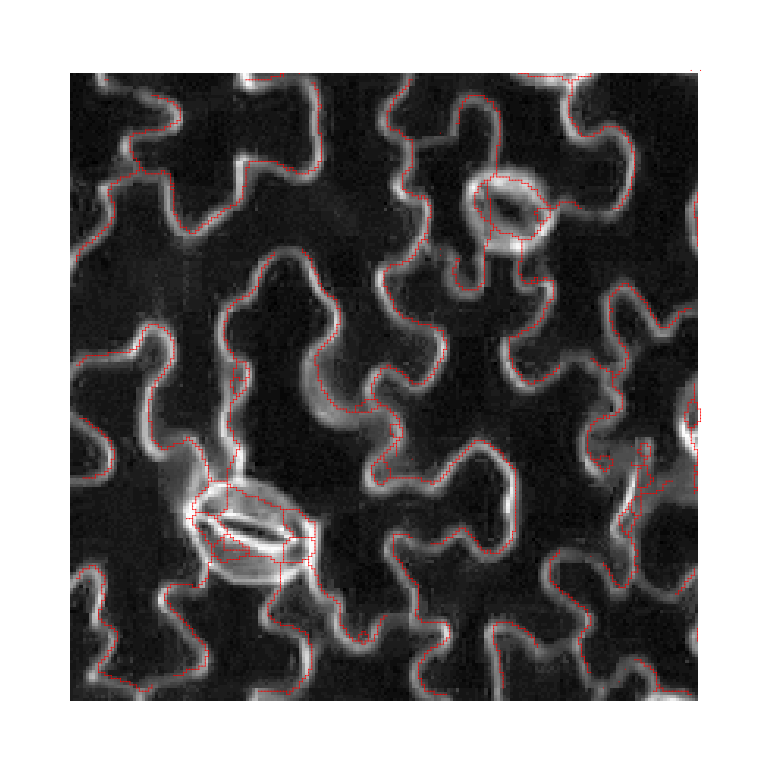
{13.5372,-Graphics-}

```mathematica
showCC2DImg[thin[cc1,{{5,.5},{∞,1}}],img1]//AbsoluteTiming
```

```mathematica
img2=Reverse[ImportGray["M2/filament_part.png"]];
cc2=buildCC2D[threshold[img2,0.238]];
```

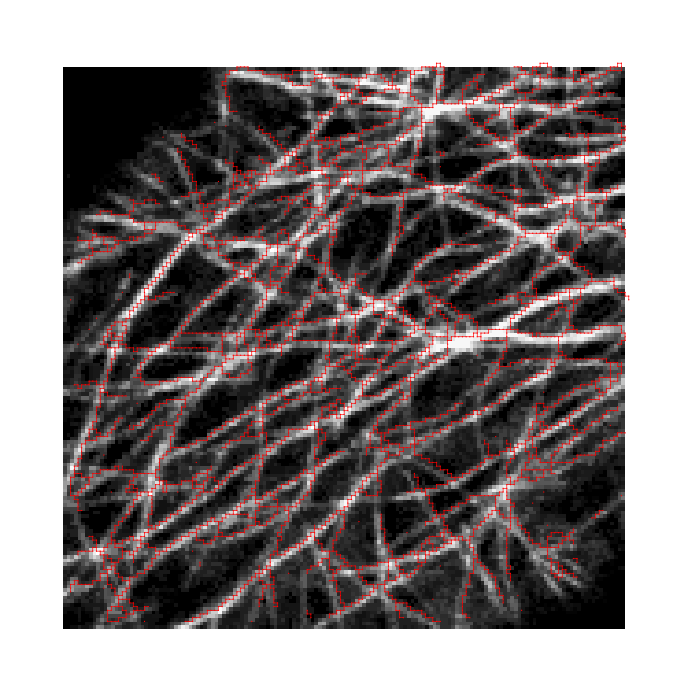
{19.6893,-Graphics-}

```mathematica
showCC2DImg[thin[cc2,{{5,.5},{Infinity,1}}],img2]//AbsoluteTiming
```

```mathematica
img3=Get["M2/hand.dat"];
cc3=buildCC3D2[img3];//AbsoluteTiming
```

{16.0021,Null}

```mathematica
showCC3D[thin[cc3,{{6,.3},{5,.4}}],cc3]//AbsoluteTiming
```

{41.3452,-Graphics3D-}

```mathematica
showCC3D[thin[cc3,{{Infinity,1},{5,.4}}],cc3]//AbsoluteTiming
```

{45.8363,-Graphics3D-}

```mathematica
showCC3D[thin[cc3,{{3,.6},{Infinity,1}}],cc3]//AbsoluteTiming
```

{44.3792,-Graphics3D-}